```mathematica
(*(**Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
(*Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)*)
Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP Windows Vers.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];*)
Import["https://qtechtheory.org/questlink.m"]
(* Search for existing files that match the pattern "quest_link*" *)
(*With[{questLinkFiles=Sort@FileNames["quest_link*",{NotebookDirectory[]}]}
,
If[Length[questLinkFiles]>0,
(* If one or more matching files are found, use the first one alphabetically *)
Print["Using the existing link file: ",First@questLinkFiles];
CreateLocalQuESTEnv[First@questLinkFiles];
,
(*If no matching files are found, download the link file*)
Print["No link file found, download quest_link"];
CreateDownloadedQuESTEnv[];
];
]*)
CreateDownloadedQuESTEnv[];
(*Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd Custom Gates.wl"]*)
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd CG V2.wl"]
```

```mathematica
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd Custom Gates.wl"]
```

```mathematica
?QuEST`Gate`*
```

```mathematica
locs2=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}];
Options[RydbergHub]={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locs2
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 10
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.007
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
```

```mathematica
Dev=RydbergHub[];
PlotAtoms[Dev,ImageSize->300,BaseStyle->Directive[18,FontFamily->"Times"]]
```

-Graphics3D-

```mathematica
CZG
```

CZG

```mathematica
?U
```

```mathematica
Cir={}
CalcCircuitMatrix[Subscript[CZG, 0,1]/.RydbergHub[][Aliases]]//MatrixForm
CalcCircuitMatrix[Subscript[CZH, 0,1]/.RydbergHub[][Aliases]]//MatrixForm
CalcCircuitMatrix[Subscript[CCZ, 0,1,2]/.RydbergHub[][Aliases]]//MatrixForm

InsertCircuitNoise[{Subscript[CZG, 0,1]},Dev]
InsertCircuitNoise[{Subscript[CZH, 0,1]},Dev]
InsertCircuitNoise[{Subscript[CCZ, 0,1,2]},Dev]
```

{}

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{{0,{UNonNorm_(0,1)[{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[2.19375×10^-6],Deph_2[4.36241×10^-7],Depol_3[2.19375×10^-6],Deph_3[4.36241×10^-7],Depol_4[2.19375×10^-6],Deph_4[4.36241×10^-7],Depol_5[2.19375×10^-6],Deph_5[4.36241×10^-7],Depol_6[2.19375×10^-6],Deph_6[4.36241×10^-7],Depol_7[2.19375×10^-6],Deph_7[4.36241×10^-7],Depol_8[2.19375×10^-6],Deph_8[4.36241×10^-7]}},{1.3,{},{}}}

{{0,{UNonNorm_(0,1)[{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[5.0625×10^-7],Deph_2[1.00671×10^-7],Depol_3[5.0625×10^-7],Deph_3[1.00671×10^-7],Depol_4[5.0625×10^-7],Deph_4[1.00671×10^-7],Depol_5[5.0625×10^-7],Deph_5[1.00671×10^-7],Depol_6[5.0625×10^-7],Deph_6[1.00671×10^-7],Depol_7[5.0625×10^-7],Deph_7[1.00671×10^-7],Depol_8[5.0625×10^-7],Deph_8[1.00671×10^-7]}},{0.3,{},{}}}

{{0,{UNonNorm_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-0.996917+0.048583 ⅈ,0,0,0,0,0,0},{0,0,-0.996917+0.048583 ⅈ,0,0,0,0,0},{0,0,0,-0.997086+0.020677 ⅈ,0,0,0,0},{0,0,0,0,-0.996917+0.048583 ⅈ,0,0,0},{0,0,0,0,0,-0.997086+0.020677 ⅈ,0,0},{0,0,0,0,0,0,-0.997086+0.020677 ⅈ,0},{0,0,0,0,0,0,0,-0.995911+0.0278531 ⅈ}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[0.],Deph_2[0.],Depol_3[2.19375×10^-6],Deph_3[4.36241×10^-7],Depol_4[2.19375×10^-6],Deph_4[4.36241×10^-7],Depol_5[2.19375×10^-6],Deph_5[4.36241×10^-7],Depol_6[2.19375×10^-6],Deph_6[4.36241×10^-7],Depol_7[2.19375×10^-6],Deph_7[4.36241×10^-7],Depol_8[2.19375×10^-6],Deph_8[4.36241×10^-7]}},{1.3,{},{}}}

```mathematica
A=CreateDensityQureg[2]
InitZeroState[A]
ApplyCircuit[A,{Subscript[X, 1],Subscript[X, 0],Subscript[UNonNorm, 0,1][{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}]}]
CalcProbOfAllOutcomes[A,{0,1}]
```

18

18

{}

{0.,0.,0.,0.997202}

```mathematica
?CalcProbOfAllOutcomes
```

```mathematica
{{0,{Subscript[UNonNorm, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}]},{Subscript[Depol, 0][0.],Subscript[Deph, 0][0.],Subscript[Depol, 1][0.],Subscript[Deph, 1][0.],Subscript[Depol, 2][2.1937467916399722*^-6],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Depol, 3][2.1937467916399722*^-6],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Depol, 4][2.1937467916399722*^-6],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Depol, 5][2.1937467916399722*^-6],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Depol, 6][2.1937467916399722*^-6],[4.3624142043174885*^-7],Subscript[Depol, 7][2.1937467916399722*^-6],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Depol, 8][2.1937467916399722*^-6],Subscript[Deph, 8][4.3624142043174885*^-7]}},{1.3,{},{}}}
```

{{0,{UNonNorm_(0,1)[{{{1,0,0,0},{0,-0.998487+0.0408016 ⅈ,0,0},{0,0,-0.998487+0.0408016 ⅈ,0},{0,0,0,-0.998348+0.0470809 ⅈ}}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[5.0625×10^-7],Deph_2[1.00671×10^-7],Depol_3[5.0625×10^-7],Deph_3[1.00671×10^-7],Depol_4[5.0625×10^-7],Deph_4[1.00671×10^-7],Depol_5[5.0625×10^-7],Deph_5[1.00671×10^-7],Depol_6[5.0625×10^-7],Deph_6[1.00671×10^-7],Depol_7[5.0625×10^-7],Deph_7[1.00671×10^-7],Depol_8[5.0625×10^-7],Deph_8[1.00671×10^-7]}},{0.3,{},{}}}

{{0,{UNonNorm_(0,1,2)[{{{1,0,0,0,0,0,0,0},{0,-0.996917+0.048583 ⅈ,0,0,0,0,0,0},{0,0,-0.996917+0.048583 ⅈ,0,0,0,0,0},{0,0,0,-0.997086+0.020677 ⅈ,0,0,0,0},{0,0,0,0,-0.996917+0.048583 ⅈ,0,0,0},{0,0,0,0,0,-0.997086+0.020677 ⅈ,0,0},{0,0,0,0,0,0,-0.997086+0.020677 ⅈ,0},{0,0,0,0,0,0,0,-0.995911+0.0278531 ⅈ}}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[0.],Deph_2[0.],Depol_3[2.19375×10^-6],Deph_3[4.36241×10^-7],Depol_4[2.19375×10^-6],Deph_4[4.36241×10^-7],Depol_5[2.19375×10^-6],Deph_5[4.36241×10^-7],Depol_6[2.19375×10^-6],Deph_6[4.36241×10^-7],Depol_7[2.19375×10^-6],Deph_7[4.36241×10^-7],Depol_8[2.19375×10^-6],Deph_8[4.36241×10^-7]}},{1.3,{},{}}}

```mathematica
Subscript[CCZ, 0,1,2]
```

CCZ_(0,1,2)

```mathematica
CalcCircuitMatrix[Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{}

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
RydbergHub[][Aliases]
```

{Init_(VQD`Private`q_Integer):>{Damp_(VQD`Private`q)[1]},SRot_(VQD`Private`q$_Integer)[VQD`Private`phi$_,VQD`Private`delta$_,VQD`Private`tg$_]:>{U_(VQD`Private`q$)[VQD`Private`unitaryDetuning[VQD`Private`phi$,VQD`Private`delta$,VQD`Private`tg$,1]]},CZ_(VQD`Private`p_Integer,VQD`Private`q_Integer)[VQD`Private`phi_]:>{U_(VQD`Private`p,VQD`Private`q)[{{1,0,0,0},{0,ⅇ^(ⅈ VQD`Private`phi),0,0},{0,0,ⅇ^(ⅈ VQD`Private`phi),0},{0,0,0,ⅇ^(ⅈ (2 VQD`Private`phi-π))}}]},CZG_(VQD`Private`p_Integer,VQD`Private`q_Integer):>{U_(VQD`Private`p,VQD`Private`q)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}]},CZH_(VQD`Private`p_Integer,VQD`Private`q_Integer):>{U_(VQD`Private`p,VQD`Private`q)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}]},SWAPLoc_(VQD`Private`q1_Integer,VQD`Private`q2_Integer):>{},Wait_(VQD`Private`q__)[VQD`Private`t_]:>{},ShiftLoc_(VQD`Private`q__)[VQD`Private`v_]:>{},C_(VQD`Private`c_Integer)[Z_(VQD`Private`t__Integer)]:>Table[C_(VQD`Private`c)[Z_(VQD`Private`targ)],{VQD`Private`targ,{VQD`Private`t}}],CCZ_(VQD`Private`p_Integer,VQD`Private`q_Integer,VQD`Private`r_Integer):>CCZ_(VQD`Private`p,VQD`Private`q,VQD`Private`r)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}],C_(VQD`Private`c__Integer)[Z_(VQD`Private`t_Integer)]:>{C_(VQD`Private`c)[Z_(VQD`Private`t)]}}

```mathematica
(*userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);*)
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]

(*This is Incorrect, and has NOT been implemented*)
MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
(*Single qubit gates transpiled using Qiskit procedure into x,y rotations*)
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}
```

```mathematica
(*Native Rydberg CCZ gate decomposed into ARP CZ and Native Single Qubit Rotations*)
Subscript[CCZDecomp,t_,c1_,c2_]:=Flatten[{XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t], Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t],Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],TGate[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1],TGate[c2],Tdg[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1]}]
(*DrawCircuit[ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2],RydDev,ReplaceAliases->True]]]*)
(*(*I hope this hasn't been used subsequently*)
CliffCCZRyd={HXTrans[0],HXTrans[0],Table[XTrans[i],{i,1,8}],Subscript[CCZ, 0,6,1],HXTrans[6],Subscript[CCZ, 7,6,2],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,5,4] XHTrans[8],Subscript[CCZ, 8,7,3]}
(*3 Qubit Grover Iteration, this can be neglected*)
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Join[Position[Reverse[SearchSeed][[1]],1],Position[Reverse[SearchSeed][[2;;]],0]]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]*)
(*C5X, C5Z, transpiled into native Rydberg gates using ARP CCZ, Ancilla 6,7,8*)
(*C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];*)
```

```mathematica
(*Direct ARP CCZ Oracle generation procedure, 6 Data qubits + 3 ancilla.*)
GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
(*Direct ARP CCZ Grover Diffusion Operator*)
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];
```

```mathematica
(*Generate empty array for data storage*)
RenormList2Q=Table[{},{i,1,4}]

(*Decomposed CCZ via ARP CZ gate Grover Oracle Generation*)
GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

(*Decomposed CCZ via ARP CZ gate Grover Diffusion Operator*)
GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

(*Decomposed CCZ, Variable Iteration Number Grover Alg Application Routine*)
GroverAlg6D3AVaryIt2Q[SearchSeed_]:=Flatten[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q}]
Init9=Table[Subscript[Init, i],{i,0,8}];
GroverDataUnNormCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],Dev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[SearchSeed],Dev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList2Q[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,(*8*)8}],{j,1,(*64*)4}]
```

{{},{},{},{}}

$Aborted

```mathematica
Init9=Table[Subscript[Init, i],{i,0,8}];
RenormList2QOldVers={{},{},{},{}}
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,
ExtractCircuit[InsertCircuitNoise[Flatten[{(*Init9,*)Table[HTrans[i],{i,0,5}]}],Dev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,OldVersCirc];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList2QOldVers[[1]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,(*8*)8}]
```

{{},{},{},{}}

{{0.110682,0.0121231,0.0125151,0.00957611,0.0154035,0.0108619,0.0121805,0.00878431,0.0133054,0.0102066,0.0128852,0.00913497,0.0122829,0.0106101,0.0130244,0.00956541,0.0115462,0.00943396,0.0110804,0.00773283,0.0111297,0.00950699,0.0112758,0.00805285,0.0111706,0.00954543,0.0122116,0.00886241,0.0117164,0.0101258,0.012812,0.00950792,0.0124316,0.0103289,0.0112696,0.00801685,0.0115651,0.010013,0.0111983,0.0080004,0.0116736,0.0103091,0.0124425,0.00906588,0.0118919,0.0102818,0.0124674,0.00918228,0.0107223,0.00900029,0.0106137,0.00748161,0.0106371,0.00906829,0.0109148,0.00780226,0.0109531,0.00937298,0.0120503,0.00881417,0.011321,0.00970019,0.0124032,0.00921918},{0.220384,0.00566286,0.00664104,0.00585205,0.00858919,0.00628925,0.00637217,0.00630429,0.00689745,0.00645848,0.00579256,0.00574147,0.00627938,0.00639226,0.00594446,0.00580778,0.00635298,0.00631296,0.00608871,0.0060922,0.00616888,0.00640526,0.00600672,0.00600483,0.00602883,0.00655699,0.00566924,0.00561965,0.00605382,0.0062529,0.00582156,0.00560247,0.00583541,0.00589367,0.00621787,0.00615895,0.00599823,0.00627754,0.00627541,0.00625096,0.0058931,0.00621321,0.00571562,0.00564313,0.00619368,0.00633902,0.0060672,0.00589553,0.00587329,0.00631229,0.00600827,0.00602453,0.00608079,0.00642514,0.00597607,0.0059535,0.00594649,0.00637503,0.00553619,0.00545412,0.00604749,0.00624767,0.00580168,0.00558307},{0.290239,0.00300585,0.00376822,0.0022603,0.00617262,0.00292166,0.00310296,0.00224121,0.0041344,0.0026049,0.00382334,0.00266326,0.00332562,0.00247068,0.00317133,0.00237188,0.00333385,0.00245258,0.00312683,0.00212322,0.00299064,0.00217065,0.00285988,0.00201607,0.00288614,0.00232271,0.00350155,0.00260058,0.00306757,0.00246775,0.00318206,0.00241516,0.00389193,0.00296278,0.00303472,0.00217079,0.0030057,0.00247459,0.00268187,0.00190791,0.00302337,0.00275489,0.003602,0.00271107,0.00303201,0.00247361,0.00295288,0.00221962,0.00293589,0.00228386,0.00303904,0.00214661,0.00274405,0.00205443,0.0027898,0.00199446,0.00285094,0.00242666,0.00350765,0.00267825,0.00292624,0.00236962,0.00304722,0.00232212},{0.301908,0.000803976,0.00214275,0.000876829,0.00248334,0.00109128,0.00113494,0.00109694,0.00149606,0.00106748,0.000754423,0.000775151,0.0010229,0.000978097,0.000795528,0.000814635,0.00123309,0.00106036,0.000971331,0.000932461,0.000997487,0.00106787,0.000852202,0.000874785,0.000859841,0.00112051,0.000758802,0.000763158,0.000883888,0.000887217,0.000788439,0.000777947,0.000983251,0.000816395,0.00105011,0.000988313,0.000958578,0.00102017,0.000934987,0.000953721,0.000821049,0.000959881,0.000744421,0.000743057,0.000994241,0.000963838,0.000865595,0.000861473,0.000883779,0.0010667,0.000915064,0.000901857,0.000934093,0.00105657,0.000811523,0.000837407,0.000838836,0.00101667,0.000718532,0.000715856,0.000895434,0.000879378,0.00078936,0.000786785},{0.265385,0.000317281,0.000830112,0.000164564,0.00141577,0.000389313,0.000201006,0.000165462,0.0005452,0.000231707,0.000287158,0.000202295,0.000361403,0.000189158,0.000163351,0.000139684,0.000431037,0.000305931,0.000165647,0.000122587,0.000249632,0.000229514,0.000160446,0.000126274,0.000261882,0.000176254,0.000194321,0.000161325,0.000243611,0.000190098,0.000182648,0.000133448,0.000585149,0.000364354,0.000167848,0.000150983,0.000252447,0.000351505,0.000140246,0.000145307,0.000257741,0.000267152,0.000255778,0.000234981,0.000264387,0.000240978,0.000146274,0.0001267,0.000302889,0.000211901,0.000168854,0.000142024,0.000182047,0.000178321,0.000141968,0.000116783,0.000227667,0.000194963,0.000201993,0.000181441,0.000204561,0.00016983,0.000142732,0.00010708},{0.199277,0.000667622,0.0013668,0.000405872,0.000634457,0.000221281,0.000291629,0.000206187,0.000482401,0.000197135,0.000333242,0.000231692,0.000289921,0.000173146,0.000223292,0.000180742,0.000531291,0.000150979,0.000484896,0.000356019,0.000276928,0.000111514,0.000305475,0.000207258,0.000352109,0.000171134,0.000301278,0.000207319,0.000254323,0.000163882,0.000255936,0.000188246,0.000657882,0.000207957,0.000502387,0.000451245,0.000329914,0.000146993,0.00026151,0.000199696,0.000357541,0.000210844,0.000322568,0.000252292,0.000234852,0.000213576,0.000200071,0.0001755,0.000398379,0.000171281,0.000457464,0.000374319,0.000291934,0.000134769,0.00027866,0.000204788,0.000316336,0.000206126,0.000265644,0.000212787,0.000216078,0.0001559,0.000224726,0.000178304},{0.1286,0.00103419,0.000888162,0.000622739,0.000683179,0.000793328,0.000666269,0.000622626,0.000685174,0.000756023,0.000571633,0.000628704,0.000725921,0.000716897,0.000614363,0.000585567,0.000810443,0.000935702,0.000492474,0.000492582,0.000637328,0.000854926,0.000536767,0.000555604,0.000732835,0.000736574,0.000596398,0.000607688,0.000629417,0.000680634,0.000554195,0.000546284,0.000760493,0.000839916,0.000553773,0.000478654,0.000754572,0.000896285,0.000562481,0.00056546,0.000742445,0.000725065,0.000589909,0.000594505,0.000769195,0.00070985,0.000640111,0.000583199,0.000771883,0.000815231,0.000478743,0.000466571,0.000623874,0.000729086,0.000479081,0.00049442,0.000672583,0.000657574,0.000580085,0.000558023,0.000668012,0.000657106,0.000534582,0.000521902},{0.0683431,0.00151272,0.001765,0.00124834,0.000943678,0.000917089,0.000948788,0.000846741,0.00114043,0.000986737,0.00118031,0.000949718,0.00103746,0.00087662,0.00100051,0.000882789,0.00117848,0.00081519,0.00122566,0.00108251,0.00097472,0.000691323,0.00104767,0.000849578,0.00121855,0.000937445,0.00108439,0.000908055,0.0010331,0.000850023,0.00107346,0.000893962,0.00141443,0.000940799,0.00128052,0.00128535,0.00104263,0.000760106,0.00104458,0.000899817,0.0012012,0.000989162,0.00115553,0.000995058,0.000928658,0.000904537,0.000940505,0.000864165,0.00113549,0.000860567,0.00118981,0.00106892,0.00101937,0.000763339,0.00105257,0.000876547,0.00115069,0.000964945,0.00105956,0.000955986,0.000955684,0.000811219,0.00102205,0.000877326}}

```mathematica
ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[KetList[6][[1]]],Dev]]
```

```mathematica
RenormList2Q
```

{{0.405434,0.314829,0.243975,0.188794,0.146314,0.113613,0.0885062,0.0691394},{0.405365,0.315316,0.245088,0.190675,0.14863,0.116127,0.0909139,0.0712739},{0.40553,0.31525,0.244784,0.189991,0.14774,0.1151,0.0898999,0.0703374},{0.405461,0.315716,0.2459,0.191874,0.150108,0.117684,0.0924002,0.0725678}}

```mathematica
(*Variable Iteration Number Decomp CCZ Grover Alg Routine Data Processing*)
RenormDataVaryIt2Q=Table[{j,Mean[RenormList2Q[[All,j]]],StandardDeviation[RenormList2Q[[All,j]]]/8},{j,1,4}]
GroverDataUnnormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]/8},{j,1,4}]
(*GroverData2ndHighestUnnormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]],{i,1,(*64*)8}]]±1/(\Sqrt[8](*8*))StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]],{i,1,(*64*)8}]]},{j,1,8}]*)

GroverDataRenormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]±(1/(2*Sqrt[2])StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]])},{j,1,8}]
GroverData2ndHighestRenormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]]/RenormList2Q[[All,j]][[i]],{i,1,4}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]/RenormList2Q[[All,j]][[i]],{i,1,(*64*)4}]]/2Sqrt[2]},{j,1,8}]
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,4}]
```

{{1,0.405415,8.47044×10^-6},{2,0.315261,0.0000445736},{3,0.244966,0.0000967247},{4,0.19042,0.000155188}}

{{1,0.0560003±0.000149244},{2,0.110054±0.000322376},{3,0.143629±0.000345639},{4,0.148809±0.000240242}}

{{1,0.138131±0.0010356},{2,0.349093±0.00297898},{3,0.586341±0.00443282},{4,0.781526±0.00464542},{5,0.880364±0.00422432},{6,0.852896±0.00536701},{7,0.713651±0.00849208},{8,0.502679±0.0117883}}

{{1,0.0187538±0.00090748},{2,0.0148732±0.0000563571},{3,0.0139705±0.000353311},{4,0.0101811±0.00014614},{5,0.0096998±0.000201529},{6,0.00955531±0.000270926},{7,0.0116414±0.00020913},{8,0.0159418±0.000637895}}

{{1,0.594585±8.47044×10^-6},{2,0.684739±0.0000445736},{3,0.755034±0.0000967247},{4,0.80958±0.000155188}}

```mathematica
Sqrt[2]
```

√2

```mathematica
{{1,0.7342165303021817,0.000046994771922360685},{2,0.5744849340982545,0.0001717444242695738},{3,0.451123347756977,0.0003703137478842423},{4,0.3555850135878708,0.0005604088462322829},{5,0.28164688968026624,0.0006930493305183145},{6,0.22359555509350898,0.0007418359096738423},{7,0.17765624753819118,0.0007198130489578208},{8,0.14098756136335625,0.0006460490429438364}}
{{1,0.09794227888352602±0.0004366046275054713},{2,0.19531465860677732±0.0010725267204842565},{3,0.25808060194808136±0.0016172777305832704},{4,0.27369591263567866±0.001829080752982407},{5,0.2470972728125621±0.001629076166605243},{6,0.19531855149594124±0.0011551565779112497},{7,0.1364017126530722±0.0008014173888298147},{8,0.08364947099634348±0.0009660896007826734}}
{{1,0.01367916206606313±0.00009457660335298407},{2,0.007873510097717057±0.00005828010263764286},{3,0.005274387323751622±0.00003905481063526633},{4,0.002709317393273488±0.00003666649358089233},{5,0.001682075775781531±0.00005086468653470105},{6,0.0010526942153539392±0.0000324545300619266},{7,0.0011044411298580807±0.000019501723654524208},{8,0.0013382930099985282±0.00002225192147119094}}
{{1,0.1333986277445727±0.0006003859052693424},{2,0.34001525757208245±0.001957021859283564},{3,0.5722805829862354±0.004019648479477648},{4,0.7702825139270331±0.006228628910776905},{5,0.8783867675085683±0.007578723317595844},{6,0.8747090553792415±0.007047731738512097},{7,0.7682889576236234±0.00471900973306156},{8,0.5923664607900175±0.004711603508283483}}
{{1,0.01863063294987469±0.00012805977485824089},{2,0.013706637181934735±0.00010409624171697906},{3,0.011692434852768895±0.00008779368933741377},{4,0.007612740904468487±0.00009362056509480241},{5,0.005951172906585273±0.00016821503522622302},{6,0.004690679212063371±0.00013475751118972214},{7,0.006212206246017464±0.00010202228590102042},{8,0.009540118916010384±0.00019401412813515882}}
{{1,0.2657834696978183±0.000046994771922360685},{2,0.4255150659017455±0.0001717444242695738},{3,0.5488766522430231±0.0003703137478842423},{4,0.6444149864121291±0.0005604088462322829},{5,0.7183531103197338±0.0006930493305183145},{6,0.7764044449064911±0.0007418359096738423},{7,0.8223437524618088±0.0007198130489578208},{8,0.8590124386366438±0.0006460490429438364}}
RenormDataVaryIt2Q={{1,0.7342165303021817,3.5813907106676723*^-9},{2,0.5744849340982545,7.812354455277304*^-9},{3,0.451123347756977,1.1529312939099698*^-8},{4,0.3555850135878708,1.4382338013567163*^-8},{5,0.28164688968026624,1.6822226100152315*^-8},{6,0.22359555509350898,1.9897023196452725*^-8},{7,0.17765624753819118,2.438590391602956*^-8},{8,0.14098756136335625,3.029224370795262*^-8}}
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
{{1,0.7342165303021817,3.5813907106676723*^-9},{2,0.5744849340982545,7.812354455277304*^-9},{3,0.451123347756977,1.1529312939099698*^-8},{4,0.3555850135878708,1.4382338013567163*^-8},{5,0.28164688968026624,1.6822226100152315*^-8},{6,0.22359555509350898,1.9897023196452725*^-8},{7,0.17765624753819118,2.438590391602956*^-8},{8,0.14098756136335625,3.029224370795262*^-8}}
{{1,0.2657834696978183±3.5813907106676723*^-9},{2,0.4255150659017455±7.812354455277304*^-9},{3,0.5488766522430231±1.1529312939099698*^-8},{4,0.6444149864121291±1.4382338013567163*^-8},{5,0.7183531103197338±1.6822226100152315*^-8},{6,0.7764044449064911±1.9897023196452725*^-8},{7,0.8223437524618088±2.438590391602956*^-8},{8,0.8590124386366438±3.029224370795262*^-8}}
DestroyAllQuregs[];
```

```mathematica
RenormList=Table[{},{i,1,64}]

(*GroversAlg6D3A[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A},{j,1,8}]]]*)
(*GroverDataUnNormCCZ=Table[If[IntegerQ[i/8],Print[i]];SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3A[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
RenormList[[i]]=Renorm;
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,64}];
*)
RenormList=Table[{},{i,1,64}];
Init9=Table[Subscript[Init, i],{i,0,8}];
(*Variable Iteration Direct ARP CCZ Grover Algorithm Applier*)
GroversAlg6D3AVaryIt[SearchSeed_]:=Flatten[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A}]
GroverDataUnNormCCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3AVaryIt[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,(*64*)8}];
```

```mathematica
(*Direct ARP CCZ Grover Data Processing*)
RenormDataVaryIt=Table[{j,Mean[RenormList[[All,j]]],StandardDeviation[RenormList[[All,j]]]/(*8*)\Sqrt[8]},{j,1,8}]
GroverDataUnnormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]/(*8*)\Sqrt[8]},{j,1,8}]
GroverData2ndHighestUnnormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]],{i,1,(*64*)8}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]],{i,1,64}]]/(*8*)\Sqrt[8]},{j,1,8}]
GroverDataRenormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]/(*8*)\Sqrt[8]},{j,1,8}]
GroverData2ndHighestRenormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]]/RenormList[[All,j]][[i]],{i,1,(*64*)8}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]/RenormList[[All,j]][[i]],{i,1,64}]]/(*8*)\Sqrt[8]},{j,1,8}]
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
```

```mathematica
(*DrawCircuit[GroverOracle6D3A[KetList[6][[1]]]]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]]*)
(*ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]*)
{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}
```

```mathematica
(*Total Probability of all output states Direct ARP CCZ*)
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,3.029224370795262*^-8}}
{{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,3.029224370795262*^-8}}
(*No post-processsing! Probability of desired output state after each iteration Direct ARP CCZ*)
GroverDataUnnormVaryIt={{1,0.11319154796634216±4.1421723588787835*^-8},{2,0.2623050982668577±1.6937839360828093*^-7},{3,0.4087680394945454±3.7074603968770286*^-7},{4,0.5130018601438691±5.938901727411863*^-7},{5,0.5493890716501066±7.63541429789058*^-7},{6,0.5167841648798985±8.256081599218835*^-7},{7,0.4272879232784237±7.495978381192323*^-7},{8,0.30774247560318213±5.580811835102066*^-7}}
{{1,0.11319154796634216±4.1421723588787835*^-8},{2,0.2623050982668577±1.6937839360828093*^-7},{3,0.4087680394945454±3.7074603968770286*^-7},{4,0.5130018601438691±5.938901727411863*^-7},{5,0.5493890716501066±7.63541429789058*^-7},{6,0.5167841648798985±8.256081599218835*^-7},{7,0.4272879232784237±7.495978381192323*^-7},{8,0.30774247560318213±5.580811835102066*^-7}}
(*Highest probability of an undesired output state after each iteration Direct ARP CCZ*)
GroverData2ndHighestUnnormVaryIt={{1,0.011881666450653638±8.498384930656307*^-9},{2,0.00820126822634179±1.7664742446385857*^-8},{3,0.004834604933162689±4.8192509272621464*^-8},{4,0.0020588183523207633±6.354699614885599*^-8},{5,0.0005333542318908827±9.014025347802221*^-8},{6,0.00016060965140730194±1.1263789572844611*^-7},{7,0.0008299895330250968±1.2770863907875202*^-7},{8,0.0020873280462217363±1.5930431779499942*^-7}}
{{1,0.011881666450653638±8.498384930656307*^-9},{2,0.00820126822634179±1.7664742446385857*^-8},{3,0.004834604933162689±4.8192509272621464*^-8},{4,0.0020588183523207633±6.354699614885599*^-8},{5,0.0005333542318908827±9.014025347802221*^-8},{6,0.00016060965140730194±1.1263789572844611*^-7},{7,0.0008299895330250968±1.2770863907875202*^-7},{8,0.0020873280462217363±1.5930431779499942*^-7}}
(*Postprocessed to account for qubit loss! Probability of desired output state after each iteration Direct ARP CCZ*)
GroverDataRenormVaryIt={{1,0.13292159178516474±4.8146121522287254*^-8},{2,0.3400362567434216±2.1661012800023092*^-7},{3,0.585434083128625±5.227891823130775*^-7},{4,0.8115957545266411±9.237734559623163*^-7},{5,0.9592218664674655±1.3083864910188895*^-6},{6,0.9942336350669329±1.5539459155519585*^-6},{7,0.9041462935062571±1.5432721011049241*^-6},{8,0.7151610472149355±1.2504886319537253*^-6}}
{{1,0.13292159178516474±4.8146121522287254*^-8},{2,0.3400362567434216±2.1661012800023092*^-7},{3,0.585434083128625±5.227891823130775*^-7},{4,0.8115957545266411±9.237734559623163*^-7},{5,0.9592218664674655±1.3083864910188895*^-6},{6,0.9942336350669329±1.5539459155519585*^-6},{7,0.9041462935062571±1.5432721011049241*^-6},{8,0.7151610472149355±1.2504886319537253*^-6}}
(*POSTPROCESSED! Highest probability of an undesired output state after each iteration Direct ARP CCZ*)GroverData2ndHighestRenormVartIt={{1,0.013952720375828419±1.00063617074977*^-8},{2,0.010631621598901774±2.2926846787748007*^-8},{3,0.006924079754007015±6.906704410192204*^-8},{4,0.003257158236500212±1.0055483251565255*^-7},{5,0.0009312253705990334±1.573909680040996*^-7},{6,0.0003089946025499827±2.1670615823031924*^-7},{7,0.0017562676574191262±2.702624825540732*^-7},{8,0.004850730172483585±3.704327694138095*^-7}}
{{1,0.013952720375828419±1.00063617074977*^-8},{2,0.010631621598901774±2.2926846787748007*^-8},{3,0.006924079754007015±6.906704410192204*^-8},{4,0.003257158236500212±1.0055483251565255*^-7},{5,0.0009312253705990334±1.573909680040996*^-7},{6,0.0003089946025499827±2.1670615823031924*^-7},{7,0.0017562676574191262±2.702624825540732*^-7},{8,0.004850730172483585±3.704327694138095*^-7}}
PLossVaryIt={{1,0.14843370105528897±3.5813907106676723*^-9},{2,0.22859667736934408±7.812354455277304*^-9},{3,0.3017693173760526±1.1529312939099698*^-8},{4,0.36790963077134253±1.4382338013567163*^-8},{5,0.4272554756574387±1.6822226100152315*^-8},{6,0.4802185858021687±1.9897023196452725*^-8},{7,0.5274128464109079±2.438590391602956*^-8},{8,0.5696878670903075±3.029224370795262*^-8}}
{{1,0.14843370105528897±3.5813907106676723*^-9},{2,0.22859667736934408±7.812354455277304*^-9},{3,0.3017693173760526±1.1529312939099698*^-8},{4,0.36790963077134253±1.4382338013567163*^-8},{5,0.4272554756574387±1.6822226100152315*^-8},{6,0.4802185858021687±1.9897023196452725*^-8},{7,0.5274128464109079±2.438590391602956*^-8},{8,0.5696878670903075±3.029224370795262*^-8}}
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,0.3029224370795262*^-8}}
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
{{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,3.029224370795262*^-9}}
{{1,0.14843370105528897±3.5813907106676723*^-9},{2,0.22859667736934408±7.812354455277304*^-9},{3,0.3017693173760526±1.1529312939099698*^-8},{4,0.36790963077134253±1.4382338013567163*^-8},{5,0.4272554756574387±1.6822226100152315*^-8},{6,0.4802185858021687±1.9897023196452725*^-8},{7,0.5274128464109079±2.438590391602956*^-8},{8,0.5696878670903075±3.029224370795262*^-9}}
```

```mathematica
ListLinePlot[{GroverDataUnnormVaryIt,GroverDataRenormVaryIt,GroverDataUnnormVaryIt2Q,GroverDataRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{Blue,Red,Green,Orange},FrameLabel->{"Number of Grover Iterations","Mean Probability of Intended Result"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"},{Left,Top}]]
ListLinePlot[{GroverData2ndHighestUnnormVaryIt,GroverData2ndHighestRenormVaryIt,GroverData2ndHighestUnnormVaryIt2Q,GroverData2ndHighestRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Blue,Dashed},{Red,Dashed},{Green,Dashed},{Orange,Dashed}},FrameLabel->{"Number of Grover Iterations"," Mean Highest Probability of Unintended Result"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"},{Right,Top}]]
ListLinePlot[{PLossVaryIt,PLossVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],FrameLabel->{"Number of Grover Iterations","Probability of Qubit Loss"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ","Decomposed CCZ"},{Right,Bottom}]]
```

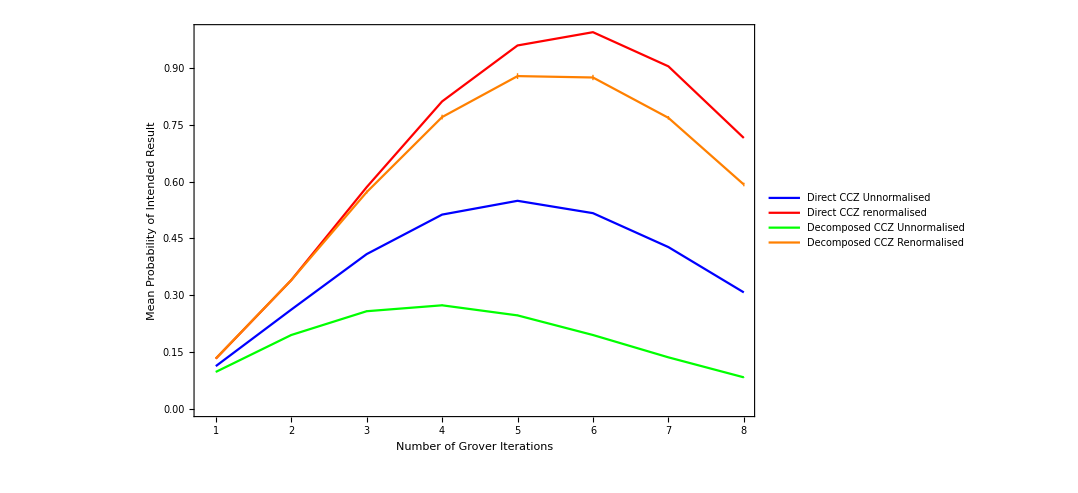

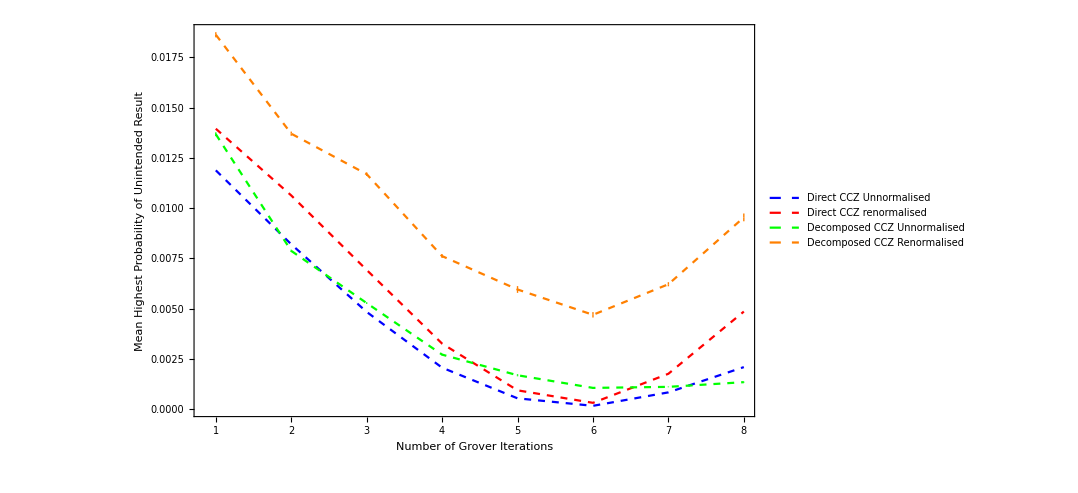

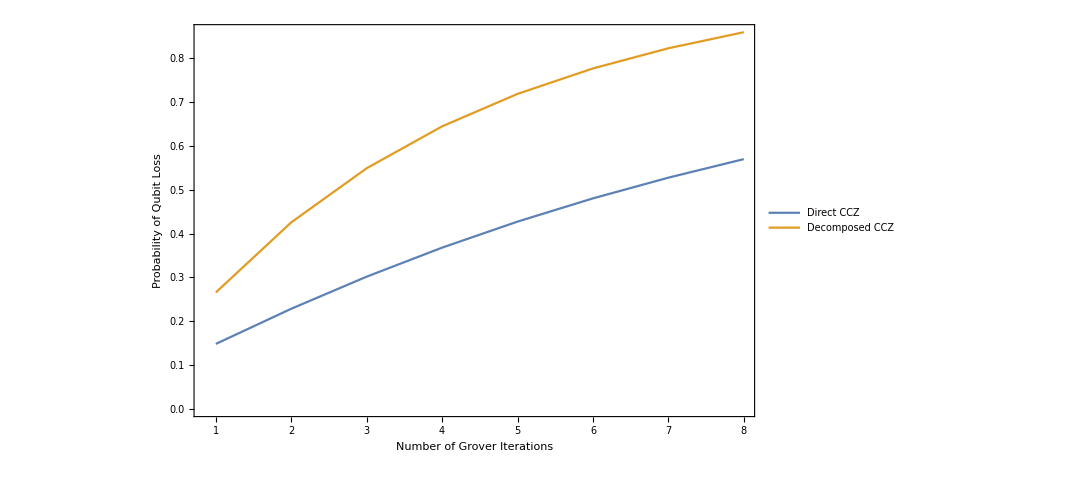
```mathematica
-Graphics-
RenormList
{0.45839509607132056,0.4583955395307735,0.45839515218830673,0.45839505760522703,0.4583952413121788,0.4583955677747983,0.458395297429273,0.4583952028460292,0.4583953044372078,0.4583956309015129,0.4583953605543335,0.4583952659713572,0.4583954496785561,0.4583957761454822,0.45839550579578975,0.45839541121264904,0.4583951595992555,0.4583954860596383,0.4583952157163937,0.4583951211340386,0.4583953048390858,0.4583956313020894,0.4583953609563316,0.45839526637381306,0.4583953679638119,0.45839569442850114,0.45839542408109024,0.4583953294988378,0.4583955132041312,0.45839583967144204,0.4583955693215182,0.4583954747391015,0.45839515959925514,0.4583954860596384,0.458395215716394,0.45839512113403835,0.4583953048390861,0.4583956313020899,0.45839536095633204,0.45839526637381245,0.45839536796381164,0.458395694428501,0.4583954240810899,0.45839532949883777,0.458395513204132,0.4583958396714422,0.45839556932151776,0.4583954747391016,0.4583955599363551,0.45839588640659945,0.4583956160536828,0.45839552147145235,0.45839570517823297,0.45839603165109766,0.4583957612956684,0.45839566671327414,0.4583957683038394,0.45839609477838883,0.4583958244213068,0.4583957298391795,0.45839591354620723,0.4583962400233773,0.4583959696637818,0.4583958750814907}
```

```mathematica
?QuEST`Gate`*
```

```mathematica
Rho=CreateDensityQureg[2]
InitZeroState[Rho];
C1={Subscript[X, 0],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}]}
ApplyCircuit[Rho,C1];
CalcProbOfAllOutcomes[Rho,{0,1}]
InitZeroState[Rho];
C2={Subscript[X, 0],Subscript[UNonNorm, 0,1][{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}]}
ApplyCircuit[Rho,C2];
CalcProbOfAllOutcomes[Rho,{0,1}]
DestroyAllQuregs[];
```

0

{X_0,KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}]}

{0.,0.998001,0.,0.}

{X_0,UNonNorm_(0,1)[{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}]}

{0.,0.998001,0.,0.}

```mathematica
OldVersCirc={Subscript[Rx, 0][π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Rx, 6][π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Rx, 7][π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Rx, 8][π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Ry, 1][-π/4],Subscript[Deph, 1][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][7.90668666872385*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[KrausNonTP, 1,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][9.087124236417665*^-8],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 0][-π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 1][π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Ry, 1][π/4],Subscript[Deph, 1][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 1,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Ry, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][0.],Subscript[Deph, 2][6.1798373002242*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][6.1798373002242*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][9.087124236417665*^-8],Subscript[Deph, 1][9.087124236417665*^-8],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 0][π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][6.1798373002242*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][6.1798373002242*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 6][π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Ry, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[KrausNonTP, 8,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][6.1798373002242*^-7],Subscript[Deph, 8][6.1798373002242*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][9.087124236417665*^-8],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][6.1798373002242*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][6.1798373002242*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[KrausNonTP, 7,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][9.087124236417665*^-8],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Ry, 3][-π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][7.90668666872385*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 7][π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Ry, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 7,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[KrausNonTP, 8,4][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][0.],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,5][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,4][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 4][-π/4],Subscript[Deph, 4][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][7.90668666872385*^-7],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,5][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[KrausNonTP, 4,5][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][9.087124236417665*^-8],Subscript[Deph, 5][9.087124236417665*^-8],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Rx, 5][π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Ry, 5][-π/4],Subscript[Deph, 5][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][7.90668666872385*^-7],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Rx, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Rx, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 4][π/4],Subscript[Deph, 4][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 4,5][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[KrausNonTP, 8,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][0.],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][7.90668666872385*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[KrausNonTP, 4,5][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][9.087124236417665*^-8],Subscript[Deph, 5][9.087124236417665*^-8],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Rx, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][9.087124236417665*^-8],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][9.087124236417665*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 4][π/4],Subscript[Deph, 4][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Rx, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][7.90668666872385*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[KrausNonTP, 7,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][9.087124236417665*^-8],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Ry, 3][-π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][7.90668666872385*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 7][π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 7,3][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 6][π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[KrausNonTP, 0,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Ry, 1][-π/4],Subscript[Deph, 1][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][7.90668666872385*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[KrausNonTP, 1,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][9.087124236417665*^-8],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 0][-π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 1][π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Ry, 1][π/4],Subscript[Deph, 1][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Rx, 0][π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 1,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Ry, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][9.087124236417665*^-8],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Ry, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 0][π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][6.1798373002242*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][6.1798373002242*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 1][π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Rx, 1][π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][0.],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][9.087124236417665*^-8],Subscript[Deph, 1][9.087124236417665*^-8],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 0][π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Deph, 0][7.90668666872385*^-7],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][9.087124236417665*^-8],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 6][π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Ry, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[KrausNonTP, 3,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][6.1798373002242*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][6.1798373002242*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][9.087124236417665*^-8],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 3][π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 3,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][6.1798373002242*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][6.1798373002242*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][-π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 3,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 3,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[KrausNonTP, 7,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][9.087124236417665*^-8],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][7.90668666872385*^-7],Subscript[Ry, 3][-π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Ry, 7][π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 7,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Ry, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 7][-π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[KrausNonTP, 4,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][6.1798373002242*^-7],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][0.],Subscript[Deph, 8][6.1798373002242*^-7],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 4][-π/4],Subscript[Deph, 4][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 4,5][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][0.],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Rx, 5][π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Ry, 5][-π/4],Subscript[Deph, 5][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][7.90668666872385*^-7],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Rx, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 4][π/4],Subscript[Deph, 4][4.1946306983398074*^-8],Subscript[Ry, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Rx, 5][-π],Subscript[Deph, 5][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 4,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[KrausNonTP, 5,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][9.087124236417665*^-8],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][9.087124236417665*^-8],Subscript[Rx, 4][-π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Ry, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Rx, 5][-π],Subscript[Deph, 5][1.6778520672833253*^-7],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][7.90668666872385*^-7],Subscript[Ry, 4][-π/4],Subscript[Deph, 4][4.1946306983398074*^-8],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 5][π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 4][-π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Ry, 5][π/4],Subscript[Deph, 5][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Ry, 4][π/2],Subscript[Deph, 4][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][0.],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Rx, 4][π],Subscript[Deph, 4][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][0.],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 5][-π],Subscript[Deph, 5][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][0.],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 5,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 5][-π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 5][-π],Subscript[Deph, 5][1.6778520672833253*^-7],Subscript[KrausNonTP, 3,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][6.1798373002242*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][0.],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][6.1798373002242*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Ry, 5][π/2],Subscript[Deph, 5][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][0.],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Rx, 5][π],Subscript[Deph, 5][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][0.],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 3,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][-π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 3,8][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Ry, 8][-π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][7.90668666872385*^-7],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 3][π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 3,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[KrausNonTP, 8,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][9.087124236417665*^-8],Subscript[Rx, 3][-π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 3][-π/4],Subscript[Deph, 3][4.1946306983398074*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 8][π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 3][-π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Ry, 8][π/4],Subscript[Deph, 8][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 3][π/2],Subscript[Deph, 3][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][0.],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Rx, 3][π],Subscript[Deph, 3][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][0.],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[KrausNonTP, 8,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Ry, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][0.],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][6.1798373002242*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][6.1798373002242*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 8][π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Rx, 8][π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 8][-π/2],Subscript[Deph, 8][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][0.],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Rx, 8][-π],Subscript[Deph, 8][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][7.90668666872385*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][0.],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 2][π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 2,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][4.3624142043174885*^-7],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][9.087124236417665*^-8],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 7][π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Ry, 7][-π/4],Subscript[Deph, 7][4.1946306983398074*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][7.90668666872385*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 2][-π/4],Subscript[Deph, 2][4.1946306983398074*^-8],Subscript[Rx, 7][-π/2],Subscript[Deph, 7][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Ry, 6][π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Ry, 2][π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][0.],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 2][π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Ry, 2][-π/2],Subscript[Deph, 2][8.389261041408247*^-8],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 6,7][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Rx, 2][-π],Subscript[Deph, 2][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][0.],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][6.1798373002242*^-7],Subscript[Deph, 7][6.1798373002242*^-7],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 7][π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][0.],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 6][-π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Rx, 7][π],Subscript[Deph, 7][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][0.],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 6][π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 6][π],Subscript[Deph, 6][1.6778520672833253*^-7],Subscript[Deph, 0][1.054224611274357*^-6],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][0.],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][2.6355636123520654*^-7],Subscript[Deph, 2][2.6355636123520654*^-7],Subscript[Deph, 3][2.6355636123520654*^-7],Subscript[Deph, 4][2.6355636123520654*^-7],Subscript[Deph, 5][2.6355636123520654*^-7],Subscript[Deph, 6][2.6355636123520654*^-7],Subscript[Deph, 7][2.6355636123520654*^-7],Subscript[Deph, 8][2.6355636123520654*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,1][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][4.3624142043174885*^-7],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Ry, 1][-π/4],Subscript[Deph, 1][4.1946306983398074*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][7.90668666872385*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Ry, 0][π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Deph, 0][2.6355636123520654*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Deph, 0][0.],Subscript[Deph, 1][1.054224611274357*^-6],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][1.054224611274357*^-6],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[KrausNonTP, 0,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][4.3624142043174885*^-7],Subscript[Deph, 2][4.3624142043174885*^-7],Subscript[Deph, 3][4.3624142043174885*^-7],Subscript[Deph, 4][4.3624142043174885*^-7],Subscript[Deph, 5][4.3624142043174885*^-7],Subscript[Deph, 6][0.],Subscript[Deph, 7][4.3624142043174885*^-7],Subscript[Deph, 8][4.3624142043174885*^-7],Subscript[Ry, 0][-π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[KrausNonTP, 1,6][{{{1,0,0,0},{0,-0.9985644285724264+0.029497152232434657 ⅈ,0,0},{0,0,-0.9985644285724264+0.029497152232434657 ⅈ,0},{0,0,0,-0.9986}}}],Subscript[Deph, 0][0.],Subscript[Deph, 1][9.087124236417665*^-8],Subscript[Deph, 2][5.271125834704904*^-7],Subscript[Deph, 3][5.271125834704904*^-7],Subscript[Deph, 4][5.271125834704904*^-7],Subscript[Deph, 5][5.271125834704904*^-7],Subscript[Deph, 6][9.087124236417665*^-8],Subscript[Deph, 7][5.271125834704904*^-7],Subscript[Deph, 8][5.271125834704904*^-7],Subscript[Rx, 0][-π],Subscript[Deph, 0][1.6778520672833253*^-7],Subscript[Ry, 1][-π/2],Subscript[Deph, 1][8.389261041408247*^-8],Subscript[Rx, 6][π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Deph, 0][0.],Subscript[Deph, 1][5.271125834704904*^-7],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][5.271125834704904*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Rx, 0][π/2],Subscript[Deph, 0][8.389261041408247*^-8],Subscript[Rx, 1][-π],Subscript[Deph, 1][1.6778520672833253*^-7],Subscript[Ry, 6][-π/4],Subscript[Deph, 6][4.1946306983398074*^-8],Subscript[Deph, 0][5.271125834704904*^-7],Subscript[Deph, 1][0.],Subscript[Deph, 2][1.054224611274357*^-6],Subscript[Deph, 3][1.054224611274357*^-6],Subscript[Deph, 4][1.054224611274357*^-6],Subscript[Deph, 5][1.054224611274357*^-6],Subscript[Deph, 6][7.90668666872385*^-7],Subscript[Deph, 7][1.054224611274357*^-6],Subscript[Deph, 8][1.054224611274357*^-6],Subscript[Ry, 0][-π/4],Subscript[Deph, 0][4.1946306983398074*^-8],Subscript[Rx, 6][-π/2],Subscript[Deph, 6][8.389261041408247*^-8],Subscript[Rx, 1][π/2],Subscript[Deph, 1][8.3892610414
```

{Rx_0[π],Deph_0[1.67785×10^-7],Rx_6[π],Deph_6[1.67785×10^-7],Rx_7[π],Deph_7[1.67785×10^-7],Rx_8[π],Deph_8[1.67785×10^-7],Ry_2[-π/2],9438,Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}
 |  |  |  |

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[Init, 0]},Dev,ReplaceAliases->True]]
```

{Damp_0[1],KrausNonTP_0[{{{0.964365,0},{0,1}}}],Deph_0[0.],Deph_1[0.000100661],Deph_2[0.000100661],Deph_3[0.000100661],Deph_4[0.000100661],Deph_5[0.000100661],Deph_6[0.000100661],Deph_7[0.000100661],Deph_8[0.000100661]}